## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[23]
```

{23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Topic

### Definition / Theorem

### This is text.

### Example

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,11}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -1/2
5 | 1/2
6 | -1/3
7 | 1/3
8 | -2
9 | 2
10 | -1/5
11 | 1/5

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,21,31}]//tf
```

21 | 1/10
22 | -1/11
23 | 1/11
24 | -2/3
25 | 2/3
26 | -1/13
27 | 1/13
28 | -1/14
29 | 1/14
30 | -1/15
31 | 1/15

```mathematica
nNaturalToQuotient[101]
```

5/2

```mathematica
nQuotientToNatural[4]
nQuotientToNatural[9]
nQuotientToNatural[25]
```

33

163

1251

```mathematica
FactorInteger[1251]
```

{{3,2},{139,1}}

## Framework for Sets

Here is one idea. Convert the set expression into an equivalent boolean expression, use BooleanMinimize to simplify the boolean expression, and then convert back to a set expression.

Set expression

Rather than using Union and Intersection, I will use the built-in symbols SquareUnion and SquareIntersection so that I don’t have to modify Union and Intersection to work with atomic symbols. So, here are the symbols I will be allowing for set expressions:

union: SquareUnion (A⊔B)
intersection: SquareIntersection (A⊓B)
subset: SquareSubset (A⊏B)
superset: SquareSuperset (A⊐B)
set difference: Backslash (A∖B)
set complement: OverBar (A.af)
set equivalence: Equal
empty set: EmptySet (∅)
universal set: UniversalSet (U)

Check the following code with the code above... then Choose how to implement.

```mathematica
MakeBoxes[EmptySet,form_]^=TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)];
MakeBoxes[UniversalSet,form_]^=TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)];

CurrentValue[EvaluationNotebook[],InputAliases]={"su"->"⊔","si"->"⊓","sb"->"⊏","sp"->"⊐","es"->TemplateBox[{},"EmptySet",DisplayFunction->("∅"&),InterpretationFunction->("EmptySet"&)],"us"->TemplateBox[{},"UniversalSet",DisplayFunction->(StyleBox["𝕌",FontFamily->"Times"]&),InterpretationFunction->("UniversalSet"&)]};

toBoolean[expr_]:=ReplaceAll[expr,{SquareUnion->Or,SquareIntersection->And,SquareSubset->Implies,SquareSuperset->Reverse@*Implies,OverBar->Not,Backslash->(And[#1,!#2]&),Equal->Equivalent,EmptySet->False,UniversalSet->True}]

setQ[EmptySet]=True;
setQ[UniversalSet]=True;
setQ[_Symbol]=True;

setQ[(Backslash|SquareUnion|SquareIntersection|OverBar)[a__]]:=AllTrue[{a},setQ]

setQ[_]=False;

fromBoolean[expr_]:=ReplaceAll[expr,{Or->SquareUnion,And->SquareIntersection,Not->OverBar,Equivalent->Equal}]
fromBoolean[a_&&!b_Symbol]:=Backslash[a,b]
fromBoolean[!a_Symbol&&b_]:=Backslash[b,a]
fromBoolean[a_||!b_Symbol]:=SquareSubset[b,a]
fromBoolean[!a_Symbol||b_]:=SquareSubset[a,b]

Options[SetSimplify]={Method->Automatic};

SetSimplify[set_,cond_:True,OptionsPattern[]]:=Module[{res},res=fromBoolean@BooleanMinimize[toBoolean[set],toBoolean[cond],Method->OptionValue[Method]];
If[setQ[set],res/. {False->EmptySet,True->UniversalSet},res]]
```

## Tmp-1

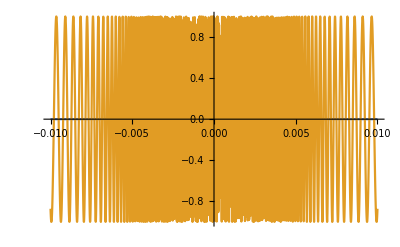

```mathematica
f[x_]:=x^2 Sin[1/x]
f[0]:=0
Plot[{f[x],f'[x]},{x,-0.01,0.01}]
```

```mathematica
PrimeOmega[1/36 25 49 144]
```

6

```mathematica
FactorInteger[1225/36][[All,2]]//Total
```

0